```mathematica
dateMouseSessionListV1={{"010621","Mouse23332","Session1"},{"010821","Mouse23332","Session2"},{"011321","Mouse23332","Session1"},{"011821","Mouse23332","Session1"},{"121420","Mouse23312","Session2"},{"121020","Mouse23312","Session4"},{"111120","Mouse23385","Session1"},{"111820","Mouse23385","Session1"},{"120320","Mouse23385","Session2"},{"092720","Mouse21068","Session1"},{"092920","Mouse21068","Session1"},{"092220","Mouse23336","Session1"},{"072520","Mouse21036","Session2"},{"080920","Mouse21036","Session1"},{"081120","Mouse21036","Session1"},{"081320","Mouse21036","Session2"},{"080820","Mouse21019","Session2"},{"081120","Mouse21019","Session1"},{"080620","Mouse21062","Session1"},{"031621","Mouse23324","Session2"},{"030921","Mouse23324","Session4"},{"030821","Mouse23321","Session1"},{"031121","Mouse23321","Session2"},{"031621","Mouse23321","Session2"}};
```

```mathematica
dateMouseSessionListV2m={{"011721","Mouse23390","Session2"},{"011821","Mouse23390","Session2"},{"010321","Mouse23382","Session1"},{"010621","Mouse23382","Session2"},{"111420","Mouse23383","Session3"},{"111720","Mouse23383","Session1"},{"112120","Mouse23383","Session2"},{"120520","Mouse23383","Session2"},{"092620","Mouse21069","Session2"},{"093020","Mouse21069","Session2"},{"092020","Mouse21011","Session2"},{"090420","Mouse21076","Session1"},{"090520","Mouse21076","Session2"},{"022821","Mouse23390","Session1"},{"030421","Mouse23390","Session1"},{"021721","Mouse23338","Session1"},{"031621","Mouse23338","Session1"},{"031821","Mouse23338","Session2"},{"021821","Mouse23310","Session1"},{"022621","Mouse23310","Session2"},{"030221","Mouse23310","Session1"},{"031121","Mouse23310","Session1"},{"031921","Mouse23310","Session2"}};
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S3A****************) 
(**********************************************)
```

```mathematica
meanDFFzOnsetV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/meanDFFzTraceOnset_V1.txt","List"];
```

```mathematica
semDFFzOnsetV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/semDFFzTraceOnset_V1.txt","List"];
```

```mathematica
meanDFFzOffsetV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/meanDFFzTraceOffset_V1.txt","List"];
```

```mathematica
semDFFzOffsetV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/semDFFzTraceOffset_V1.txt","List"];
```

```mathematica
meanDFFzOnsetV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/meanDFFzTraceOnset_V2m.txt","List"];
```

```mathematica
semDFFzOnsetV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/semDFFzTraceOnset_V2m.txt","List"];
```

```mathematica
meanDFFzOffsetV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/meanDFFzTraceOffset_V2m.txt","List"];
```

```mathematica
semDFFzOffsetV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/semDFFzTraceOffset_V2m.txt","List"];
```

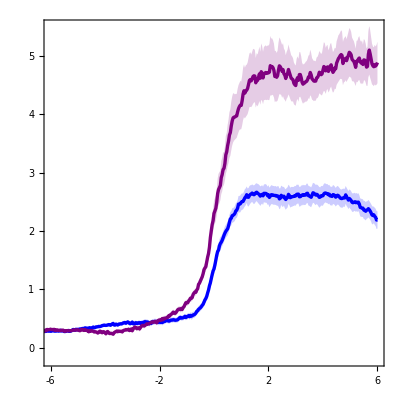

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFzOnsetV1,Part[#,2]&/@meanDFFzOnsetV1+(Part[#,2]&/@semDFFzOnsetV1),Part[#,2]&/@meanDFFzOnsetV1-(Part[#,2]&/@semDFFzOnsetV1),Part[#,2]&/@meanDFFzOnsetV2m,Part[#,2]&/@meanDFFzOnsetV2m+(Part[#,2]&/@semDFFzOnsetV2m),Part[#,2]&/@meanDFFzOnsetV2m-(Part[#,2]&/@semDFFzOnsetV2m)},Filling->{1->{{2},Directive[Opacity[0.2],Blue]},1->{{3},Directive[Opacity[0.2],Blue]},4->{{5},Directive[Opacity[0.2],Purple]},4->{{6},Directive[Opacity[0.2],Purple]}},PlotStyle->{{Blue,Thickness[0.006]},Transparent,Transparent,{Purple,Thickness[0.006]},Transparent,Transparent,{Darker@Orange,Thickness[0.006]},Transparent,Transparent,{Darker@Yellow,Thickness[0.006]},Transparent,Transparent},DataRange->{-15,6},PlotRange->{{-6,6},{-0.2,5.5}},FrameTicks->{{LinTicks[-0.2,5.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-6,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

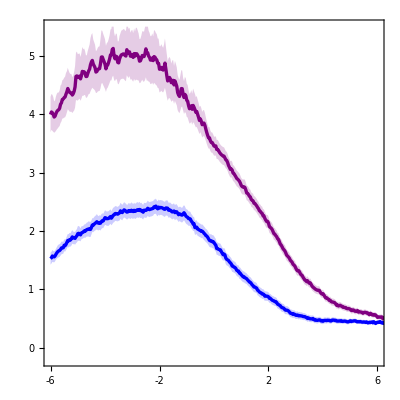

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFzOffsetV1,Part[#,2]&/@meanDFFzOffsetV1+(Part[#,2]&/@semDFFzOffsetV1),Part[#,2]&/@meanDFFzOffsetV1-(Part[#,2]&/@semDFFzOffsetV1),Part[#,2]&/@meanDFFzOffsetV2m,Part[#,2]&/@meanDFFzOffsetV2m+(Part[#,2]&/@semDFFzOffsetV2m),Part[#,2]&/@meanDFFzOffsetV2m-(Part[#,2]&/@semDFFzOffsetV2m)},Filling->{1->{{2},Directive[Opacity[0.2],Blue]},1->{{3},Directive[Opacity[0.2],Blue]},4->{{5},Directive[Opacity[0.2],Purple]},4->{{6},Directive[Opacity[0.2],Purple]}},PlotStyle->{{Blue,Thickness[0.006]},Transparent,Transparent,{Purple,Thickness[0.006]},Transparent,Transparent,{Darker@Orange,Thickness[0.006]},Transparent,Transparent,{Darker@Yellow,Thickness[0.006]},Transparent,Transparent},DataRange->{-6,15},PlotRange->{{-6,6},{-0.2,5.5}},FrameTicks->{{LinTicks[-0.2,5.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-6,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

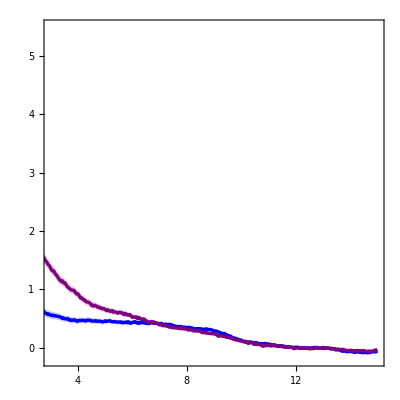

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFzOffsetV1,Part[#,2]&/@meanDFFzOffsetV1+(Part[#,2]&/@semDFFzOffsetV1),Part[#,2]&/@meanDFFzOffsetV1-(Part[#,2]&/@semDFFzOffsetV1),Part[#,2]&/@meanDFFzOffsetV2m,Part[#,2]&/@meanDFFzOffsetV2m+(Part[#,2]&/@semDFFzOffsetV2m),Part[#,2]&/@meanDFFzOffsetV2m-(Part[#,2]&/@semDFFzOffsetV2m)},Filling->{1->{{2},Directive[Opacity[0.2],Blue]},1->{{3},Directive[Opacity[0.2],Blue]},4->{{5},Directive[Opacity[0.2],Purple]},4->{{6},Directive[Opacity[0.2],Purple]}},PlotStyle->{{Blue,Thickness[0.006]},Transparent,Transparent,{Purple,Thickness[0.006]},Transparent,Transparent,{Darker@Orange,Thickness[0.006]},Transparent,Transparent,{Darker@Yellow,Thickness[0.006]},Transparent,Transparent},DataRange->{-6,15},PlotRange->{{3,15},{-0.2,5.5}},FrameTicks->{{LinTicks[-0.2,5.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[3,15,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S3B****************) 
(**********************************************)
```

```mathematica
locModValsV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/locModIndexSummVals_V1.txt","List"];
```

```mathematica
locModValsV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/locModIndexSummVals_V2m.txt","List"];
```

```mathematica
v1Charts=Show[BoxWhiskerChart[locModValsV1,{{"Whiskers", Directive[Blue,Thick]}, {"Fences", Directive[Blue,Thick]},{"MedianMarker", Directive[Blue,Thickness[0.009]]}},PlotRange->{All,{-1.2,1}},ChartStyle->Directive[Blue,Opacity[0.3]],Frame->False],DistributionChart[locModValsV1,PlotRange->{All,{-1.2,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Blue],Frame->False],FrameTicks->{{LinTicks[-1.2,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
pmCharts=Show[BoxWhiskerChart[locModValsV2m,{{"Whiskers", Directive[Purple,Thick]}, {"Fences", Directive[Purple,Thick]},{"MedianMarker", Directive[Purple,Thickness[0.009]]}},PlotRange->{All,{-1.2,1}},ChartStyle->Directive[Purple,Opacity[0.3]],Frame->False],DistributionChart[locModValsV2m,PlotRange->{All,{-1.2,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Purple],Frame->False],FrameTicks->{{LinTicks[-1.2,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[locModValsV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{-1.2,1}},ChartStyle->Transparent,Frame->False],DistributionChart[locModValsV2m,PlotRange->{All,{-1.2,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-1.2,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

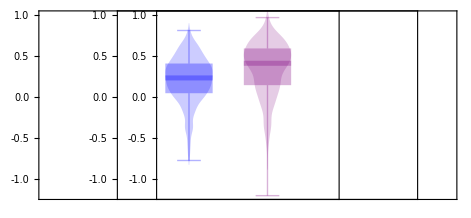

```mathematica
GraphicsRow[{v1Charts,pmCharts,transp},Spacings->{{-280,-280,-320}}]
```